```mathematica
(*Heat transfer with ambiant air*)
ϕ = 10^-3;
Cpa =1000;
β = 1/(273.15+30);
σ = 5.67 10^-8;
λa = 0.026;
μa = 1.9 10^-5;
ρa = 1.2 ;
νa = μa/ρa;
ϵ = 0.85;
αa = λa/(ρa Cpa);
Tair = 273.15+20;
Tnerf =  273.15+50;
Pr =νa/αa;
Ray = (9.81 β ϕ^3 (Tnerf-Tair))/(νa αa);
Nu =((0.6 + 0.387 Ray^(1/6))/((1+(0.559/Pr)^(9/16))^(8/27)))^2;
(Nu λa)/ϕ
(π d 1)/((π d^2)/4 1)
(2 1 1)/(1 1 d)
σ (Tnerf^2+Tair^2)(Tnerf+Tair)
```

20.2338

4/d

2/d

6.65208

```mathematica
λ = 0.76;
ρ = 1030;
h = 2 27;
Cp = 3500;
α = λ/(ρ Cp);
ϕ = 10^-3;
L = 0.5 10^-2;
dp = 400 10^-6;(*diamètre du pulse*)
tp = 10 400 10^-6;(*durée du pulse*)
f = 10;(*fréquence de pulse*)
Ep = 4 10^-3;(*énergie du pulse*)
xp = (L-dp)/2;(*position axiale du début du pulse*)
Vt = dp (π ϕ^2)/4;(*volume de la tranche*)
δ = 0.35;(*fraction de la tranche du nerf cylindrique dans laquelle le pulse arrive*)
e[t_] = Ep/(tp δ Vt)If[Mod[t,1/f]<tp,1,0];
m = 30;
Troom = 20;
Tini = 28;
```

```mathematica
ratio=L/ϕ;
Δ = ϕ/m;
Bi = (Δ h)/λ;
αt = α/Δ^2;
L/Δ
n =Round[L/Δ,1];
npd=Round[xp/Δ,1];
npf = Round[(xp+dp)/Δ,1];
mpd = Round[(ϕ -dp)/Δ,1];
```

150.

```mathematica
index[x_]:=If[x<=n/2,Round[(m-1)-(x-npd)((m-1)-mpd)/(n/2-npd),1],Round[mpd+(x-n/2)((m-1)-mpd)/(npf-n/2),1]];
Table[index[x],{x,npd,npf}]
```

{29,27,25,24,22,20,18,20,22,24,25,27,29}

```mathematica
mpd
```

18

```mathematica
inc = {};
For[i=1,i<n,i++,
inc = Join[inc,Table[T[i,j][t],{j,1,m-1}]];
]
ci = {};
For[i=1,i<npd,i++,
ci = Join[ci,Table[T[i,j][0]==Tini,{j,1,m-1}]];
]
For[i=npd,i<=npf,i++,
ci = Join[ci,Table[T[i,j][0]==Tini,{j,1,mpd-1}]];
ci = Join[ci,Table[T[i,j][0]==Tini,{j,mpd,m-1}]];
]
For[i=npf+1,i<n,i++,
ci = Join[ci,Table[T[i,j][0]==Tini,{j,1,m-1}]];
]
bc = Table[T[i,0][t]->(T[i,1][t]+Bi Troom)/(1+Bi),{i,1,n-1}];
bc = Join[bc,Table[T[i,m][t]->(T[i,m-1][t]+Bi Troom)/(1+Bi),{i,1,n-1}]];
bc = Join[bc,Table[T[0,j][t]->T[1,j][t],{j,1,m-1}]];
bc = Join[bc,Table[T[n,j][t]->T[n-1,j][t],{j,1,m-1}]];
```

```mathematica
eq = {};
For[i=1,i<npd,i++,
eq = Join[eq,Table[T[i,j]'[t]== αt (T[i+1,j][t]+T[i-1,j][t]-2T[i,j][t]+T[i,j+1][t]+T[i,j-1][t]-2T[i,j][t]),{j,1,m-1}]];
];
For[i=npd,i<=npf,i++,
eq = Join[eq,Table[T[i,j]'[t]== αt (T[i+1,j][t]+T[i-1,j][t]-2T[i,j][t]+T[i,j+1][t]+T[i,j-1][t]-2T[i,j][t]),{j,1,index[i]-1}]];
eq = Join[eq,Table[T[i,j]'[t]== αt (T[i+1,j][t]+T[i-1,j][t]-2T[i,j][t]+T[i,j+1][t]+T[i,j-1][t]-2T[i,j][t])+1/(ρ Cp)Ep/(tp δ Vt)If[Mod[t,1/f]<tp,1,0],{j,index[i],m-1}]];
];
For[i=npf+1,i<n,i++,
eq = Join[eq,Table[T[i,j]'[t]== αt (T[i+1,j][t]+T[i-1,j][t]-2T[i,j][t]+T[i,j+1][t]+T[i,j-1][t]-2T[i,j][t]),{j,1,m-1}]];
];
eqfull = Join[eq,ci]/.bc;
sol=NDSolve[eqfull,inc,{t,0,3}][[1]];
```

```mathematica
Contour[temps_]:=(
datafull = {};
bcbis = {T[0,0][t]->T[0,1][t],T[0,m][t]->T[0,m-1][t],T[n,0][t]->T[n,1][t],T[n,m][t]->T[n,m-1][t]};
For[i = 0, i<= n, i++,
datafull = Join[datafull,Table[{1000 i Δ,1000j Δ,T[i,j][t]/.bcbis/.bc/.sol/.t->temps},{j,0,m}]];
];
buff=ListContourPlot[datafull,Frame -> True ,PlotRange ->All, Axes -> False, FrameLabel->{"x (mm)","y (mm)"},BaseStyle->{FontFamily->"Times",FontSize->12},ColorFunctionScaling->False,PlotRange->All,InterpolationOrder->3,Contours->20,ColorFunction->ColorData[{"Rainbow",{Troom,60}}],ImageSize->700,AspectRatio->m/n,PlotLabel->"T (°C)",ContourLines-> False];
Legended[buff,BarLegend[{"Rainbow",{Troom,60}}]]
)
```

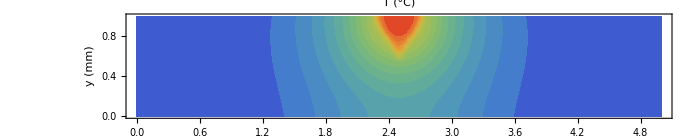

```mathematica
Contour[2+tp]
```

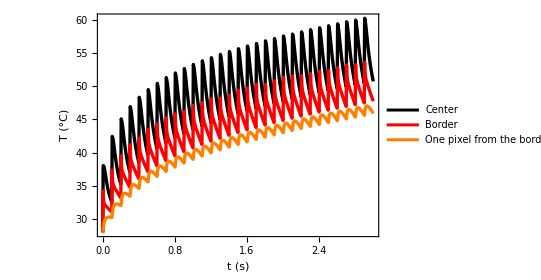

```mathematica
pix = 0.073 10^-3;
Tcentre[t_]=T[n/2,m][t]/.bc/.sol;
Tbord[t_]=T[npf,m][t]/.bc/.sol;
T1pix[t_]=T[npf+Floor[pix/Δ],m][t]/.bc/.sol;
Plot[Tcentre[t],{t,0,3},Axes-> False, Frame-> True,PlotRange-> All,AspectRatio->0.7,FrameLabel->{"t (s)","T (°C)"},BaseStyle->{FontFamily->"Times",FontSize->14},PlotStyle->{Black,Thickness[0.006]} , PlotLegends->Placed[LineLegend[{"Center"},LabelStyle->{11}],Right]];
Plot[Tbord[t],{t,0,3},Axes-> False, Frame-> True,PlotRange-> All,AspectRatio->0.7,FrameLabel->{"t (s)","T (°C)"},BaseStyle->{FontFamily->"Times",FontSize->14},PlotStyle->{Red,Thickness[0.006]} , PlotLegends->Placed[LineLegend[{"Border"},LabelStyle->{11}],Right]];
Plot[T1pix[t],{t,0,3},Axes-> False, Frame-> True,PlotRange-> All,AspectRatio->0.7,FrameLabel->{"t (s)","T (°C)"},BaseStyle->{FontFamily->"Times",FontSize->14},PlotStyle->{Orange,Thickness[0.006]} , PlotLegends->Placed[LineLegend[{"One pixel from the border"},LabelStyle->{11}],Right]];
Show[%%%,%%,%]
```

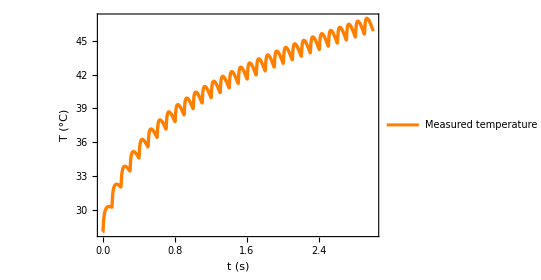

```mathematica
Plot[T1pix[t],{t,0,3},Axes-> False, Frame-> True,PlotRange-> All,AspectRatio->0.7,FrameLabel->{"t (s)","T (°C)"},BaseStyle->{FontFamily->"Times",FontSize->14},PlotStyle->{Orange,Thickness[0.006]} , PlotLegends->Placed[LineLegend[{"Measured temperature"},LabelStyle->{11}],Top]]
```

```mathematica
(*nouveaux graphes*)
```

```mathematica
depth = 0;(*profondeur en microns*)
Temp[t_]=T[n/2,m-Round[depth 10^-6/Δ,1]][t]/.bc/.sol;
data0=Table[{i,Temp[(i-1)1/f+tp]-Temp[(i-1)1/f]},{i,1,3/(1/f)-1}];
depth = 100;(*profondeur en microns*)
Temp[t_]=T[n/2,m-Round[depth 10^-6/Δ,1]][t]/.bc/.sol;
data100=Table[{i,Temp[(i-1)1/f+tp]-Temp[(i-1)1/f]},{i,1,3/(1/f)-1}];
depth = 200;(*profondeur en microns*)
Temp[t_]=T[n/2,m-Round[depth 10^-6/Δ,1]][t]/.bc/.sol;
data200=Table[{i,Temp[(i-1)1/f+tp]-Temp[(i-1)1/f]},{i,1,3/(1/f)-1}];
depth = 300;(*profondeur en microns*)
Temp[t_]=T[n/2,m-Round[depth 10^-6/Δ,1]][t]/.bc/.sol;
data300=Table[{i,Temp[(i-1)1/f+tp]-Temp[(i-1)1/f]},{i,1,3/(1/f)-1}];
depth = 400;(*profondeur en microns*)
Temp[t_]=T[n/2,m-Round[depth 10^-6/Δ,1]][t]/.bc/.sol;
data400=Table[{i,Temp[(i-1)1/f+tp]-Temp[(i-1)1/f]},{i,1,3/(1/f)-1}];
depth = 500;(*profondeur en microns*)
Temp[t_]=T[n/2,m-Round[depth 10^-6/Δ,1]][t]/.bc/.sol;
data500=Table[{i,Temp[(i-1)1/f+tp]-Temp[(i-1)1/f]},{i,1,3/(1/f)-1}];
```

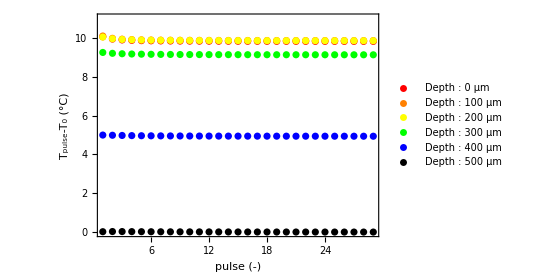

```mathematica
ListPlot[data0,Axes-> False, Frame-> True,PlotRange-> All,AspectRatio->0.7,FrameLabel->{"pulse (-)","T_pulse-T_0 (°C)"},BaseStyle->{FontFamily->"Times",FontSize->14},PlotStyle->{Red,Thickness[0.006]} , PlotLegends->Placed[LineLegend[{StringJoin["Depth : ",ToString[0], " μm"]},LabelStyle->{11}],Right]];
ListPlot[data100,Axes-> False, Frame-> True,PlotRange-> All,AspectRatio->0.7,FrameLabel->{"pulse (-)","T_pulse-T_0 (°C)"},BaseStyle->{FontFamily->"Times",FontSize->14},PlotStyle->{Orange,Thickness[0.006]} , PlotLegends->Placed[LineLegend[{StringJoin["Depth : ",ToString[100], " μm"]},LabelStyle->{11}],Right]];
ListPlot[data200,Axes-> False, Frame-> True,PlotRange-> All,AspectRatio->0.7,FrameLabel->{"pulse (-)","T_pulse-T_0 (°C)"},BaseStyle->{FontFamily->"Times",FontSize->14},PlotStyle->{Yellow,Thickness[0.006]} , PlotLegends->Placed[LineLegend[{StringJoin["Depth : ",ToString[200], " μm"]},LabelStyle->{11}],Right]];
ListPlot[data300,Axes-> False, Frame-> True,PlotRange-> All,AspectRatio->0.7,FrameLabel->{"pulse (-)","T_pulse-T_0 (°C)"},BaseStyle->{FontFamily->"Times",FontSize->14},PlotStyle->{Green,Thickness[0.006]} , PlotLegends->Placed[LineLegend[{StringJoin["Depth : ",ToString[300], " μm"]},LabelStyle->{11}],Right]];
ListPlot[data400,Axes-> False, Frame-> True,PlotRange-> All,AspectRatio->0.7,FrameLabel->{"pulse (-)","T_pulse-T_0 (°C)"},BaseStyle->{FontFamily->"Times",FontSize->14},PlotStyle->{Blue,Thickness[0.006]} , PlotLegends->Placed[LineLegend[{StringJoin["Depth : ",ToString[400], " μm"]},LabelStyle->{11}],Right]];
ListPlot[data500,Axes-> False, Frame-> True,PlotRange-> All,AspectRatio->0.7,FrameLabel->{"pulse (-)","T_pulse-T_0 (°C)"},BaseStyle->{FontFamily->"Times",FontSize->14},PlotStyle->{Black,Thickness[0.006]} , PlotLegends->Placed[LineLegend[{StringJoin["Depth : ",ToString[500], " μm"]},LabelStyle->{11}],Right]];
Show[%%%%%%,%%%%%,%%%%,%%%,%%,%,PlotRange-> {All,{0,11}}]
```

```mathematica
profil[npulse_,depth_]:=(
dist = 2 10^-3;
time1 =npulse/f;
data=Table[{10^3(i-n/2) Δ,T[i,m-Round[depth 10^-6/Δ,1]][t]/.bc/.sol/.t->time1},{i,Round[n/2-dist/Δ,1],Round[n/2+dist/Δ,1]}];
grprofile[npulse]=ListPlot[data,Joined-> True,Axes-> False, Frame-> True,PlotRange-> {All,{0,60}},AspectRatio->0.7,FrameLabel->{"z (mm)","T (°C)"},BaseStyle->{FontFamily->"Times",FontSize->14},PlotStyle->{Orange,Thickness[0.006]} , PlotLegends->Placed[LineLegend[{StringJoin["Depth : ",ToString[depth], " μm"]},LabelStyle->{11}],Right]]
)
```

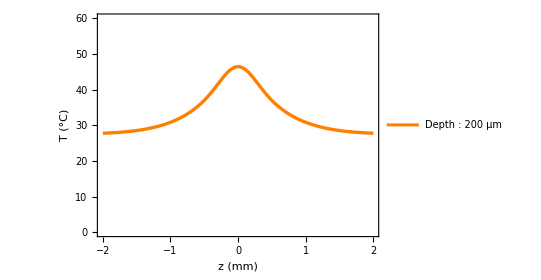

16.3853

```mathematica
profil[21,200]
prof[z_]=Interpolation[data][z];
dersec[z_] =prof''[z]; 
width =2 z/.FindRoot[dersec[z],{z,0.1}];
(prof[0]-prof[width/2])/(width/2)
```

```mathematica
(* Spatial gradient computation based on FWHM definition *)
gradientbis[npulse_,depth_]:=
(
profil[npulse,depth];
prof[z_]=Interpolation[data][z];
Thalf = (prof[0]+prof[data[[1,1]]])/2;
width =2 Abs[z/.FindRoot[prof[z]-Thalf,{z,0.1}]];
(prof[0]-prof[data[[1,1]]])/width
)
```

```mathematica
(* Spatial gradient computation based on inflexion points, which are close to HM points *)
gradient[npulse_,depth_]:=
(
profil[npulse,depth];
prof[z_]=Interpolation[data][z];
dersec[z_] =prof''[z]; 
width =2 z/.FindRoot[dersec[z],{z,0.1}];
(prof[0]-prof[width/2])/(width/2)
)
```

```mathematica
gradient[30,400]
gradientbis[30,400]
```

11.3495

13.1915

```mathematica
tevgrad[depth_]:=
(
Table[{i,gradientbis[i,depth]},{i,1,30}]
)
```

```mathematica
data0 =tevgrad[0];
data100 =tevgrad[100];
data200 =tevgrad[200];
data300 =tevgrad[300];
data400 =tevgrad[400];
```

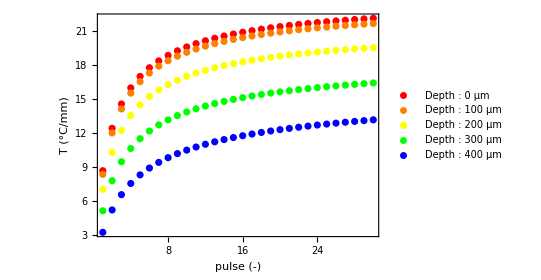

```mathematica
ListPlot[data0,Joined-> False,Axes-> False, Frame-> True,PlotRange-> All,AspectRatio->0.7,FrameLabel->{"pulse (-)","T (°C/mm)"},BaseStyle->{FontFamily->"Times",FontSize->14},PlotStyle->{Red,Thickness[0.006]} , PlotLegends->Placed[LineLegend[{StringJoin["Depth : ",ToString[0], " μm"]},LabelStyle->{11}],Right]]; (*change Joined-> False to True if willing to have full curve*)
ListPlot[data100,Joined-> False,Axes-> False, Frame-> True,PlotRange-> All,AspectRatio->0.7,FrameLabel->{"pulse (-)","gradT (°C/mm)"},BaseStyle->{FontFamily->"Times",FontSize->14},PlotStyle->{Orange,Thickness[0.006]} , PlotLegends->Placed[LineLegend[{StringJoin["Depth : ",ToString[100], " μm"]},LabelStyle->{11}],Right]];
ListPlot[data200,Joined-> False,Axes-> False, Frame-> True,PlotRange-> All,AspectRatio->0.7,FrameLabel->{"pulse (-)","gradT (°C/mm)"},BaseStyle->{FontFamily->"Times",FontSize->14},PlotStyle->{Yellow,Thickness[0.006]} , PlotLegends->Placed[LineLegend[{StringJoin["Depth : ",ToString[200], " μm"]},LabelStyle->{11}],Right]];
ListPlot[data300,Joined-> False,Axes-> False, Frame-> True,PlotRange-> All,AspectRatio->0.7,FrameLabel->{"pulse (-)","gradT (°C/mm)"},BaseStyle->{FontFamily->"Times",FontSize->14},PlotStyle->{Green,Thickness[0.006]} , PlotLegends->Placed[LineLegend[{StringJoin["Depth : ",ToString[300], " μm"]},LabelStyle->{11}],Right]];
ListPlot[data400,Joined-> False,Axes-> False, Frame-> True,PlotRange-> All,AspectRatio->0.7,FrameLabel->{"pulse (-)","gradT (°C/mm)"},BaseStyle->{FontFamily->"Times",FontSize->14},PlotStyle->{Blue,Thickness[0.006]} , PlotLegends->Placed[LineLegend[{StringJoin["Depth : ",ToString[400], " μm"]},LabelStyle->{11}],Right]];
Show[%%%%%,%%%%,%%%,%%,%,PlotRange-> All]
```